```mathematica
ClearAll["Global`*"]
```

```mathematica
S1=m1^2 χ1;
S2=m2^2 χ2;
L=η(r M^3)^(1/2);
```

```mathematica
A1=(J^2-(L-S)^2)^(1/2);
A2=((L+S)^2-J^2)^(1/2);
A3=(S^2-(S1-S2)^2)^(1/2);
A4=((S1+S2)^2-S^2)^(1/2);
```

```mathematica
ξ=Simplify[Simplify[Simplify[((J^2-L^2-S^2)(S^2(1+q)^2-(S1^2-S2^2)(1-q^2))-(1-q^2)A1 A2 A3 A4 Cos[ϕ])/(4q M^2 S^2 L)]/.{χ1->1,χ2->1}/.{η->q/(q+1)^2,m1->M/(q+1),m2->(q M)/(q+1),r->a M,J->b M^2},M>0]]/.S->x M^2/.M->1
```

1/(4 √a q^2 x^2)(1+q)^2 ((b^2-(a q^2)/(1+q)^4-x^2) (-((-1+q)^2 (1+q^2))/(1+q)^2+(1+q)^2 x^2)+(-1+q^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(((1+q^2)^2-(1+q)^4 x^2)/(1+q)^4) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2) Cos[ϕ])

```mathematica
F[x_,ϕ_,q_,a_,b_]:=1/(4 √a q^2 x^2)(1+q)^2 ((b^2-(a q^2)/(1+q)^4-x^2) (-((-1+q)^2 (1+q^2))/(1+q)^2+(1+q)^2 x^2)+(-1+q^2) √((-(-1+q)^2+(1+q)^2 x^2)/(1+q)^2) √(((1+q^2)^2-(1+q)^4 x^2)/(1+q)^4) √(b^2-(-(√a q)/(1+q)^2+x)^2) √(-b^2+((√a q)/(1+q)^2+x)^2) Cos[ϕ]);
```

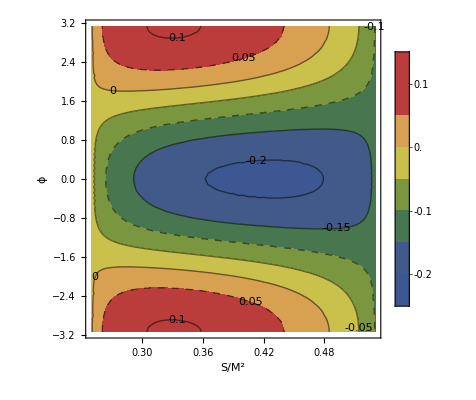

```mathematica
ContourPlot[F[x,ϕ,0.6,100,2.34],{x,0.25,0.53},{ϕ,-π,π},FrameLabel->{"S/M^2","ϕ"},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"DarkRainbow",ContourStyle->{Black,Black,Dashed}]
```